```mathematica
(*DEFINITION OF FUNCTIONS *)
ClearAll[angle,t,g,b1,b2,b3]

(*This function draws an inclined plane of variable inclination with a ball*)
inclinedPlane[angle_, t_, g_, b1_, b2_, b3_]:= 

DynamicModule[
	{θ, lengthPlane,heightPlane, h, dFall, yFall, xFall, timeFall, ϕ, ballRadius, ballCenter, ballPoint, lineBells, bellOne, bellTwo, bellThree, bellEnd},
	θ = angle * π/180;(*inclination angle of the plane in radians*)
	lengthPlane = 400;
	heightPlane = lengthPlane * Sin[θ]; (*height of the plane*)
	h = lengthPlane * Sin[θ]+2*ballRadius*Cos[θ]; (*height of the line of bells*)
    dFall = 1/2*g*Sin[θ]*t^2;(*distance falling on the plane*)
	yFall = -dFall*Sin[θ];(*vertical distance of falling*)
	xFall = dFall*Cos[θ];(*horitzontal distance of falling*)
	ballRadius=10;
	ϕ = dFall/ballRadius;(*angle rotating by the ball rolling down the plane*)
	ballCenter ={ballRadius*Sin[θ]+xFall, heightPlane+ballRadius*Cos[θ]+yFall};
	ballPoint = ballCenter + {ballRadius*Sin[θ],ballRadius*Cos[θ]};
	DynamicWrapper[	
    Graphics[
		{
		(*draws the plane*)
		Style[Line[{{0,lengthPlane*Sin[θ]},{lengthPlane*Cos[θ],0}}],Blue,Thick],

		(*draws the ball*)
		Style[Circle[ballCenter,ballRadius],Red,Thick] ,
		
		(*draws ballPoint*)
		{PointSize[Large],Red,Point[ballPoint]},
		
		(*draws the final stop mark on the plane *)		
		Style[Line[{{lengthPlane*Cos[θ],0},{lengthPlane*Cos[θ]+2*ballRadius*Sin[θ],2*ballRadius*Cos[θ]}}],Blue,Thick],

		(*draws the line for the bells *)
		lineBells = Line[{{2*ballRadius*Sin[θ],lengthPlane*Sin[θ]+2*ballRadius*Cos[θ]},{lengthPlane*Cos[θ]+2*ballRadius*Sin[θ],2*ballRadius*Cos[θ]}}],
	
		(*draws the bells *)
		PointSize[Large],
		bellEnd = Point[pointLine[1,lineBells]], (*point location of the last fixed bell*)
		bellOne = Point[pointLine[b1,lineBells]], (*point location of the first mobile bell*)
		bellTwo = Point[pointLine[b2,lineBells]], (*point location of the second mobile bell*)
		bellThree = Point[pointLine[b3,lineBells]], (*point location of the third mobile bell*)
		
		
		(*draws the radius of the ball*)
		Style[Line[{ballCenter,ballCenter+ballRadius*{-Sin[θ+ϕ],-Cos[θ+ϕ]}}],Red],

		(*draws the inclination arc of the plane*)	
		Style[Circle[{lengthPlane*Cos[θ],0},100,{π-θ,π}],Blue]					
		},
	(*plot the labels*)
	PlotLabel->Style[Row[
						{
						"θ = ",angle,"°",
						"  a = ",Round[g* Sin[θ],0.1]," m/",Superscript["s",2],
						"  t = ",Round[t,0.1],
						" t1 = ",Round[√(2*(h - bellThree[[1,2]])/(g*(Sin[θ])^2)),0.1],
						" t2 = ",Round[√(2*(h - bellTwo[[1,2]])/(g*(Sin[θ])^2)),0.1],
						" t3 = ",Round[√(2*(h - bellOne[[1,2]])/(g*(Sin[θ])^2)),0.1],
						" tf = ",Round[√(2*(lengthPlane-ballRadius)/(g*Sin[θ])),0.1],						
						}
						],
						Black,"Label",10],
	PlotRange->{{0,400},{0,300}},
	ImageSize->400,
	Frame->True
	],
	(*emits sound when the ball touch the bells*)
	If[
		EuclideanDistance[bellThree[[1]],ballPoint] < radiusFall[angle, lengthPlane, g , ballPoint[[2]], 0.04]||
		EuclideanDistance[bellTwo[[1]],ballPoint] < radiusFall[angle, lengthPlane, g , ballPoint[[2]], 0.04] ||
		EuclideanDistance[bellOne[[1]],ballPoint] < radiusFall[angle, lengthPlane, g , ballPoint[[2]], 0.04] ||
		EuclideanDistance[bellEnd[[1]],ballPoint] ≤ ballRadius 
		,
		EmitSound[Sound[SoundNote[]]]
		]
	]
];

(*This function locate a bell on the line of bells*)
ClearAll[bell,lines]
pointLine[bell_,lines_]:=
Module[{pointLine,startPoint,finalPoint,direction},
	startPoint = lines[[1,1]];
	finalPoint = lines[[1,2]];
	direction = finalPoint - startPoint;
	pointLine = startPoint + bell*direction
	];


(*This function compute the final time of falling on an inclined Plane*)
ClearAll[angle,lengthPlane,g]
timeFall[angle_,lengthPlane_,g_]:=
Module[{θ,finalTime,ballRadius},
	θ = angle * π/180;
	ballRadius = 10;
	finalTime = √(2*(lengthPlane-ballRadius)/(g*Sin[θ]))
	];
	
(*This function compute the radius of proximity between the ball and the bell to emit sound*)
ClearAll[angle,lengthPlane,δ,y]
radiusFall[angle_, lengthPlane_, g_ , y_, δ_]:=
Module[{θ,ballRadius,v,h,R},
	θ = angle * π/180;
    ballRadius=10;
	h = lengthPlane * Sin[θ]+2*ballRadius*Cos[θ]; (*height of the line of bells*)
	v = √(2*g*(h-y)); (*speed of falling on the plane*)
	R = Round[v * δ,0.01](*radius of detection between the ball and the bells for emit sound*)
	];


(*This function map a list of Solar planets taking its gravity and and its images*)
ClearAll[planets]
menuPlanet[planets_]:=
Module[{menuSolar},
		menuSolar = Map[QuantityMagnitude[UnitConvert[#["Gravity"],"SI"]]-> Row[{#,#["Image"]}]&,planets]
	]
```

```mathematica
Manipulate[

inclinedPlane[angle, t, g, b1, b2,b3],

(*configuration of controls*)
	(*the angle is measured in degrees*)
	{{angle,5,"slope θ"},5,45,5,ControlType->Slider} ,
	
	(*the position of the intermediate bells between the start and the end of the plane*)
	{{b1,0,"bell 1"},0,1,0.01,ControlType->Automatic},
	{{b2,0,"bell 2"},0,b1,0.01,ControlType->Automatic},
	{{b3,0,"bell 3"},0,b2,0.01,ControlType->Automatic},
	
		
	(*the time is in seconds*)
	{{t,0,"release ball"},0,timeFall[angle,400,g],0.01,Trigger,AnimationRate->1,Appearance->"Labeled",ControlPlacement->Left},
		
	(*gravitational constant of Solar system planets*)
	{{g,9.8`3.,"Planet:"},menuPlanet[PlanetData[]]},ControlType->PopupMenu,

		
	SaveDefinitions->True,
	ControlPlacement->Left
]
```

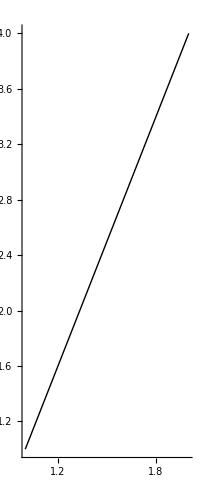

```mathematica
Graphics[Line[{{1,1},{2,4}}],Axes->{True,False} ,AxesOrigin->Automatic]
```